Project 8 - Pretty Pictures!
Jacob Schnoor


Problem 1

x(t)=t and y(t)=t^2

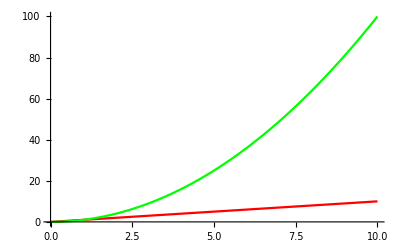

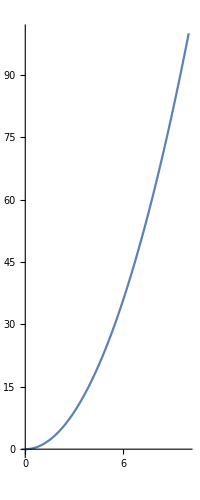

x(t)=Cos[t]+Sin[t] and y(t)=Cos[t]-Sin[t]

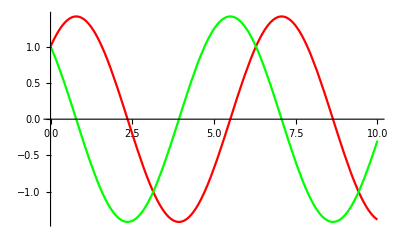

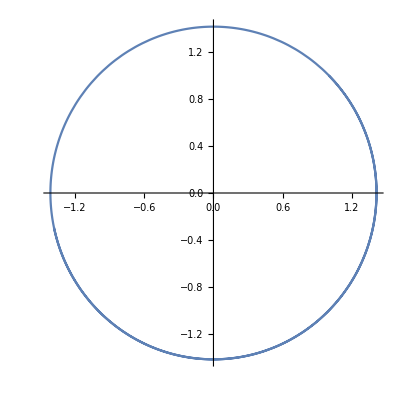

x(t)=ⅇ^-t t and y(t)=Log[t^2]

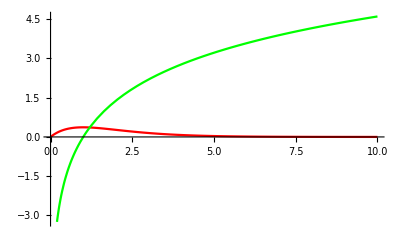

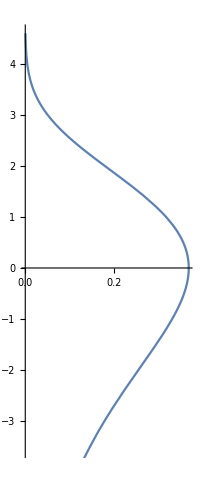

```mathematica
fx=t;
fy=t^2;
pl1=Plot[fx,{t,0,10},PlotStyle->Red];
pl2=Plot[fy,{t,0,10},PlotStyle->Green];
Print["x(t)=",fx," and y(t)=",fy,"\n"];
Show[pl1,pl2,PlotRange->All]
ParametricPlot[{fx,fy},{t,0,10}]
fx=Sin[t]+Cos[t];
fy=Cos[t]-Sin[t];
pl1=Plot[fx,{t,0,10},PlotStyle->Red];
pl2=Plot[fy,{t,0,10},PlotStyle->Green];
Print["x(t)=",fx," and y(t)=",fy,"\n"];
Show[pl1,pl2,PlotRange->All]
ParametricPlot[{fx,fy},{t,0,10}]
fx=t(ⅇ^(-t));
fy=Log[ⅇ,(t^2)];
pl1=Plot[fx,{t,0,10},PlotStyle->Red];
pl2=Plot[fy,{t,0,10},PlotStyle->Green];
Print["x(t)=",fx," and y(t)=",fy,"\n"];
Show[pl1,pl2,PlotRange->All]
ParametricPlot[{fx,fy},{t,0,10}]
```

Problem 2

-Graphics-

-Graphics-

x(t)= -2 ⅇ^(2 s) and y(t)= -ⅇ^-s (-1+2 ⅇ^(3 s))

-Graphics-

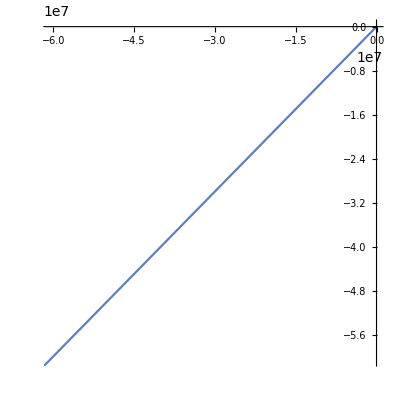

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is (-2+Log[ⅇ^C[1]]) Log[ⅇ^C[1]] == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 2-Log[ⅇ^C[1]] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

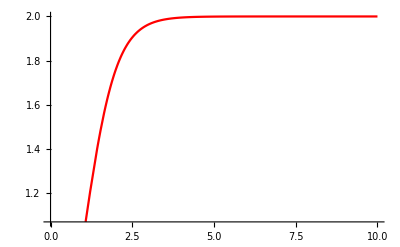

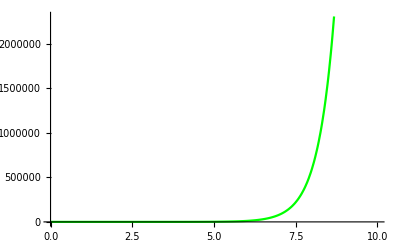

x(t)= (2 ⅇ^(2 s))/(ⅇ^2+ⅇ^(2 s)) and y(t)= (ⅇ^2+ⅇ^(2 s))/(2 ⅇ^2)

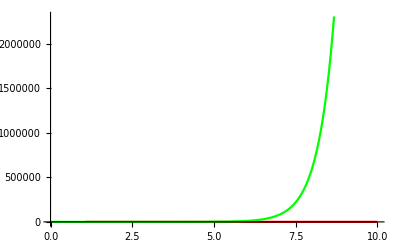

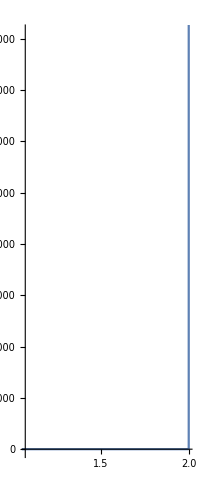

```mathematica
Clear[xed,yed];
fvect=DSolve[{xed'[s]==2xed[s],yed'[s]==3xed[s]-yed[s],xed[0]==-2,yed[0]==-1},{xed[s],yed[s]},s];
fq=fvect[[1,1,2]];
fr=fvect[[1,2,2]];
pl1=Plot[fq,{s,0,20},PlotStyle->Red]
pl2=Plot[fr,{s,0,20},PlotStyle->Green]
Print["\nx(t)= ",fq," and y(t)= ",fr,"\n"];
Show[pl1,pl2,PlotRange->All]
ParametricPlot[{fq,fr},{s,0,10}]
fvect=DSolve[{xbb'[s]==xbb[s]*ybb[s],ybb'[s]==ybb[s]/xbb[s],xbb[1]==1,ybb[1]==1},{xbb[s],ybb[s]},s];
fq=fvect[[1,1,2]];
fr=fvect[[1,2,2]];
pl1=Plot[fq,{s,0,10},PlotStyle->Red]
pl2=Plot[fr,{s,0,10},PlotStyle->Green]
Print["\nx(t)= ",fq," and y(t)= ",fr,"\n"];
Show[pl1,pl2,PlotRange->All]
ParametricPlot[{fq,fr},{s,0,10}]
```

Problem 3

a.

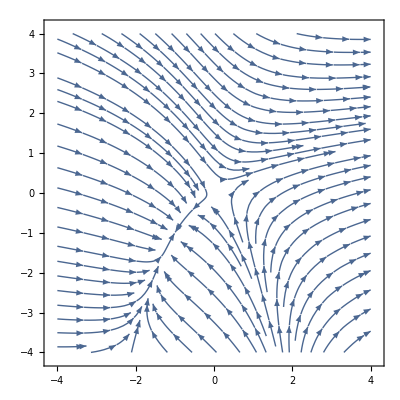

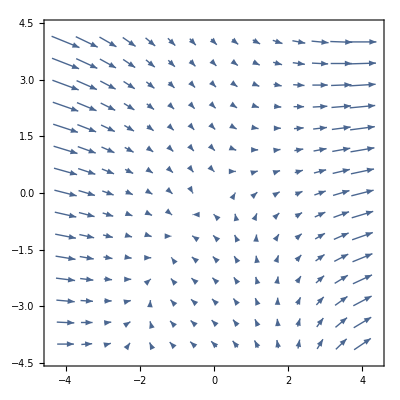

```mathematica
pl1=StreamPlot[{x'=(x^2)+y,y'=x-y},{x,-4,4},{y,-4,4}]
pl2=VectorPlot[{x'=(x^2)+y,y'=x-y},{x,-4,4},{y,-4,4}]
```

b. The stream plot is better at showing the overall shape of what a solution might look like but it sacrifices some degree of precision. The vector plot looks more like a scattered mesh and is less capable of portraying overall shape. It shines however in its precision as each vector is a straight line showing the derivative of the function at any values for x and y.

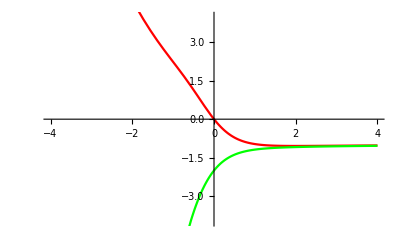

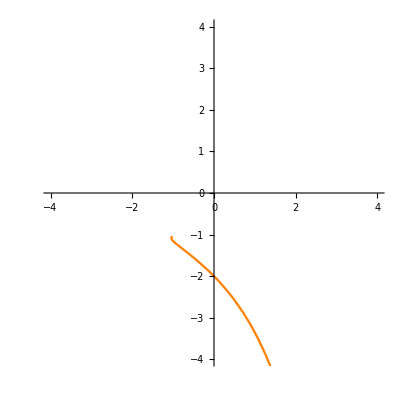

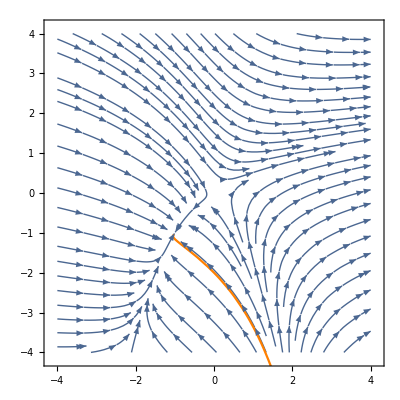

```mathematica
Clear[xed,yed];
fvect=NDSolve[{xed'[s]==(xed[s])^2+yed[s],yed'[s]==xed[s]-yed[s],xed[0]==0,yed[0]==-2},{xed[s],yed[s]},{s,-4,4}];
fq=fvect[[1,1,2]];
fr=fvect[[1,2,2]];
pl3=Plot[fq,{s,-4,4},PlotStyle->Red];
pl4=Plot[fr,{s,-4,4},PlotStyle->Green];
pl5=ParametricPlot[{fq,fr},{s,-4,4},PlotStyle->Orange];
Show[pl3,pl4,PlotRange->{{-4,4},{-4,4}}]
Show[pl5,PlotRange->{{-4,4},{-4,4}}]
Show[pl1,pl5]
```

c. As t approaches infinity, the coordinates of x and y move asymptotically toward a single point that appears to be at roughly (-1,-1) on the graph. This is because both functions approach a derivative of zero as t becomes infinitely large. With infinitesimally miniscule movement in the x and y directions, the line appears to just stop at a single point because the coordinates only become closer and closer to that one specific spot.